```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/josephcrandall/Documents/school/GW_Grad/2018_1Spring/ECE_6999_Thesis_Research/w12_04-02

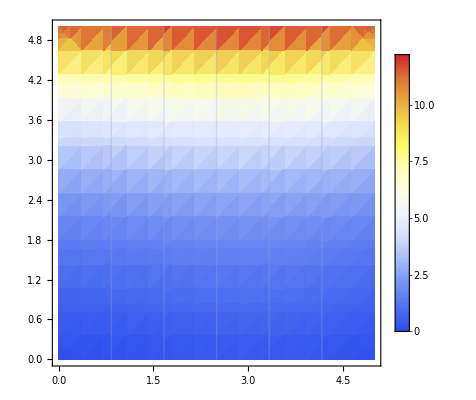

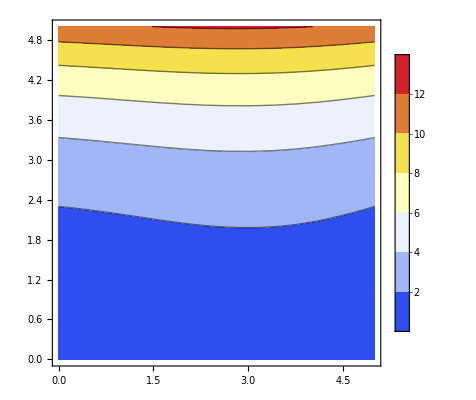

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
a=5;
b=5;
f0[x_,y_]:=x+ y;
f[x_,y_]:=f0[ x,y]/(Sinh [(π b)/a]) Sin[(π x)/a]  +Sinh[π y/a]
DensityPlot[f[x,y],{x,0,5},{y,0,5},Mesh->5, ColorFunction->"TemperatureMap",PlotLegends->Automatic]
ContourPlot[f[x,y],{x,0,5},{y,0,5}, ColorFunction->"TemperatureMap",PlotLegends->Automatic]
Plot3D[f[x,y],{x,0,5},{y,0,5},Mesh->1]  (*5^1 *) 
Plot3D[f[x,y],{x,0,5},{y,0,5},Mesh->25] (*5^2 *) 
Plot3D[f[x,y],{x,0,5},{y,0,5},Mesh->125] (*5^3 *) 
Plot3D[f[x,y],{x,0,5},{y,0,5},Mesh->625] (*5^4 *) 
(*Plot3D[f[x,y],{x,0,5},{y,0,5},Mesh->3125]*)
(*Plot3D[f[x,y],{x,0,5},{y,0,5},Mesh->15625]*)
```

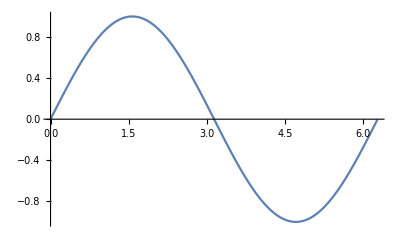

points.csv

```mathematica
points5=Table[{x,Sin[x]},{x,Range[0,2 π,.01]}];
ListLinePlot[points]
Export["points.csv",points5]
```

```mathematica
This following points are taken at the top left corner of each box
```

```mathematica
points5 = Table[{f[x,y]}, {x,Range[0,5,1]},{y,Range[0,5,1]}]//N; (*5^1 -> Step (5^-0) *) 
Export["points5.csv", points5];
points25 = Table[{f[x,y]}, {x,Range[0,5,0.2]},{y,Range[0,5,0.2]}]//N;  (*5^2 -> Step (5^-1)*)
Export["points25.csv", points25];
points125 = Table[{f[x,y]}, {x,Range[0,5,0.04]},{y,Range[0,5,0.04]}]//N;(*5^2 -> Step (5^-2)*)
Export["points125.csv", points125];
points625 = Table[{f[x,y]}, {x,Range[0,5,0.008]},{y,Range[0,5,0.008]}]//N; (*5^4* -> Step (5^-3)*)
Export["points625.csv", points625];
```